```mathematica
init={5640000,3,1,2,0,0,0};
sum=Total[init];
beta=0.45;
sigmaA=0.1;
sigmaI=0.25;
gammaA=0.25;
gammaI=0.18;
gammaH=0.18;
nu=0.02;
mu=0.01;
step=0.1;
t=225;
n=t/step;
f[y_]:={
-(beta)*(y[[1]]*(y[[3]]+y[[4]]))/sum,
(beta)*(y[[1]]*(y[[3]]+y[[4]]))/(sum-y[[5]]-y[[6]])-(sigmaA+sigmaI+nu)*y[[2]],
sigmaA*y[[2]]-gammaA*y[[3]],
sigmaI*y[[2]]-(gammaI)*y[[4]],
nu*y[[2]]-(mu+gammaH)*y[[5]],
mu*y[[5]],
gammaA*y[[3]]+gammaI*y[[4]]+gammaH*y[[5]]
};
```

```mathematica
rk4[init_,h_]:=Module[{k1,k2,k3,k4},
k1=f[init];
k2=f[init+(h/2)*k1];
k3=f[init+(h/2)*k2];
k4=f[init+h*k3];
init+(h/6)*(k1+2*k2+2*k3+k4)
];
```

```mathematica
sSet=ConstantArray[0,IntegerPart[n]+1];
eSet=ConstantArray[0,IntegerPart[n]+1];
aSet=ConstantArray[0,IntegerPart[n]+1];
iSet=ConstantArray[0,IntegerPart[n]+1];
hSet=ConstantArray[0,IntegerPart[n]+1];
dSet=ConstantArray[0,IntegerPart[n]+1];
rSet=ConstantArray[0,IntegerPart[n]+1];
{sSet[[1]],eSet[[1]],aSet[[1]],iSet[[1]],hSet[[1]],dSet[[1]],rSet[[1]]}=init;
y0=init;
Do[
y1=rk4[y0,step];
{sSet[[i+1]],eSet[[i+1]],aSet[[i+1]],iSet[[i+1]],hSet[[i+1]],dSet[[i+1]],rSet[[i+1]]}=y1;
y0=y1,
{i,1,n}];
```

```mathematica
tSet=Table[i*step,{i,0,n}];
s=Transpose[{tSet,sSet}];
e=Transpose[{tSet,eSet}];
a=Transpose[{tSet,aSet}];
i=Transpose[{tSet,iSet}];
h=Transpose[{tSet,hSet}];
d=Transpose[{tSet,dSet}];
r=Transpose[{tSet,rSet}];
```

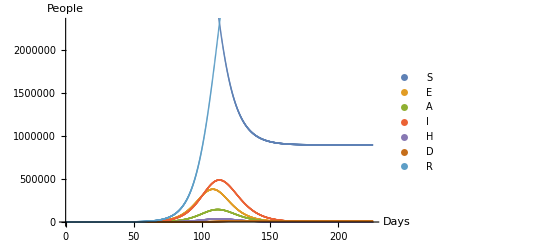

```mathematica
ListPlot[{s,e,a,i,h,d,r},AxesLabel->{"Days","People"},PlotLegends->{"S","E","A","I","H","D","R"}]
```

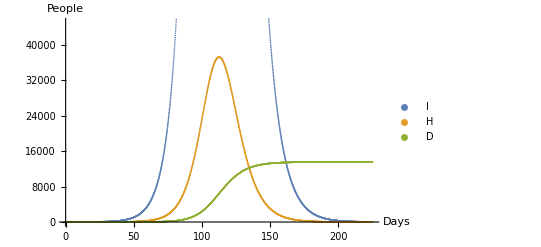

```mathematica
ListPlot[{i,h,d},AxesLabel->{"Days","People"},PlotLegends->{"I","H","D"}]
```

```mathematica
i[[101]]
Table[{tSet[[j]]+3,hSet[[j]]+iSet[[j]]},{j,1,n+1,1/step}]
```

{10.,7.8933}

{{3.,2},{4.,2.44642},{5.,2.90122},{6.,3.38204},{7.,3.90218},{8.,4.47306},{9.,5.10548},{10.,5.81042},{11.,6.5995},{12.,7.48531},{13.,8.48172},{14.,9.60414},{15.,10.8698},{16.,12.2979},{17.,13.9103},{18.,15.7312},{19.,17.7883},{20.,20.1126},{21.,22.7391},{22.,25.7075},{23.,29.0623},{24.,32.8542},{25.,37.1401},{26.,41.9847},{27.,47.4607},{28.,53.6505},{29.,60.6474},{30.,68.5564},{31.,77.4966},{32.,87.6025},{33.,99.0258},{34.,111.939},{35.,126.535},{36.,143.034},{37.,161.684},{38.,182.765},{39.,206.595},{40.,233.53},{41.,263.977},{42.,298.391},{43.,337.29},{44.,381.259},{45.,430.956},{46.,487.129},{47.,550.618},{48.,622.377},{49.,703.481},{50.,795.145},{51.,898.741},{52.,1015.82},{53.,1148.13},{54.,1297.65},{55.,1466.62},{56.,1657.54},{57.,1873.27},{58.,2117.02},{59.,2392.4},{60.,2703.5},{61.,3054.91},{62.,3451.85},{63.,3900.13},{64.,4406.37},{65.,4977.96},{66.,5623.25},{67.,6351.62},{68.,7173.61},{69.,8101.05},{70.,9147.21},{71.,10327.},{72.,11657.},{73.,13155.8},{74.,14844.3},{75.,16745.5},{76.,18885.1},{77.,21291.8},{78.,23997.1},{79.,27035.8},{80.,30446.2},{81.,34270.4},{82.,38553.9},{83.,43346.6},{84.,48701.7},{85.,54676.4},{86.,61331.6},{87.,68730.7},{88.,76939.9},{89.,86026.4},{90.,96057.7},{91.,107099.},{92.,119214.},{93.,132456.},{94.,146872.},{95.,162494.},{96.,179338.},{97.,197397.},{98.,216638.},{99.,236996.},{100.,258370.},{101.,280621.},{102.,303564.},{103.,326975.},{104.,350584.},{105.,374082.},{106.,397127.},{107.,419350.},{108.,440371.},{109.,459805.},{110.,477283.},{111.,492465.},{112.,505051.},{113.,514800.},{114.,521535.},{115.,525152.},{116.,525621.},{117.,522991.},{118.,517376.},{119.,508957.},{120.,497965.},{121.,484672.},{122.,469380.},{123.,452407.},{124.,434074.},{125.,414701.},{126.,394591.},{127.,374029.},{128.,353273.},{129.,332556.},{130.,312080.},{131.,292014.},{132.,272503.},{133.,253659.},{134.,235572.},{135.,218306.},{136.,201906.},{137.,186398.},{138.,171792.},{139.,158086.},{140.,145267.},{141.,133313.},{142.,122197.},{143.,111886.},{144.,102341.},{145.,93524.7},{146.,85396.1},{147.,77914.1},{148.,71037.6},{149.,64726.6},{150.,58941.7},{151.,53645.1},{152.,48800.7},{153.,44374.1},{154.,40332.6},{155.,36645.7},{156.,33284.6},{157.,30222.6},{158.,27434.6},{159.,24897.5},{160.,22589.8},{161.,20491.6},{162.,18584.8},{163.,16852.6},{164.,15279.3},{165.,13851.},{166.,12554.5},{167.,11378.},{168.,10310.7},{169.,9342.6},{170.,8464.63},{171.,7668.55},{172.,6946.83},{173.,6292.61},{174.,5699.67},{175.,5162.31},{176.,4675.38},{177.,4234.19},{178.,3834.48},{179.,3472.37},{180.,3144.35},{181.,2847.23},{182.,2578.12},{183.,2334.38},{184.,2113.64},{185.,1913.73},{186.,1732.7},{187.,1568.77},{188.,1420.32},{189.,1285.9},{190.,1164.19},{191.,1053.99},{192.,954.209},{193.,863.866},{194.,782.07},{195.,708.014},{196.,640.966},{197.,580.263},{198.,525.307},{199.,475.552},{200.,430.509},{201.,389.73},{202.,352.812},{203.,319.391},{204.,289.134},{205.,261.743},{206.,236.946},{207.,214.498},{208.,194.176},{209.,175.78},{210.,159.126},{211.,144.049},{212.,130.401},{213.,118.046},{214.,106.861},{215.,96.7358},{216.,87.57},{217.,79.2726},{218.,71.7613},{219.,64.9617},{220.,58.8064},{221.,53.2342},{222.,48.19},{223.,43.6238},{224.,39.4902},{225.,35.7483},{226.,32.3609},{227.,29.2945},{228.,26.5186}}